```mathematica
2+3
```

5

```mathematica
√(2.0×10π)(10./ⅇ)^10
```

3.5987×10^6

```mathematica
c = 299792458 Meter/Second;
```

```mathematica
v =c/2
```

(149896229 Meter)/Second

```mathematica
√(1-v^2/c^2)
```

(√3)/2

```mathematica
Factor[x^7-1]
```

(-1+x) (1+x+x^2+x^3+x^4+x^5+x^6)

```mathematica
TrigReduce[Sin[3θ]^5]
```

1/16 (10 Sin[3 θ]-5 Sin[9 θ]+Sin[15 θ])

```mathematica
Assuming[k∈Integers, Simplify[Sin[2π k + x]]]
```

Sin[x]

```mathematica
Times[a, Plus[b, c]]
```

a (b+c)

```mathematica
Clear[c]
FullForm[a(b+c)^-1]
```

```mathematica
Part[Part[a x^6+b x+c, 2],1]
```

b

```mathematica
(a x^6+b x+c)[[2, 1]]
```

b

```mathematica
((x^2+y)z/2)[[2,1,2]]
```

2

```mathematica
(a/b)[[2,2]]
```

-1

```mathematica
a/b // FullForm
```

Times[a,Power[b,-1]]

```mathematica
Divide[a,b]
```

a/b

```mathematica
FullForm[Divide[a,b]]//Trace
```

{{a/b,a/b},Times[a,Power[b,-1]]}

```mathematica
randLis[n_]:= RandomReal[1,{n}]
```

```mathematica
?randLis
```

Global`randLis

randLis[n_]:=RandomReal[1,{n}]

```mathematica
randLis[{1, 2, 3}]
```

RandomReal::array: The array dimensions {{1, 2, 3}} given in position 2 of RandomReal[1, {{1, 2, 3}}] should be a list of non-negative machine-sized integers giving the dimensions for the result.

RandomReal[1,{{1,2,3}}]

```mathematica
RandLis[3]
```

RandLis[3]

```mathematica
randLis[5]
```

{0.747144,0.672457,0.435939,0.28006,0.498221}

```mathematica
Table[randLis[n], {n, 1, 5}]
```

```mathematica
randLis2[n_] := (x = RandomReal[];  Table[x, {n}])
```

```mathematica
randLis[5]
```

{0.0344107,0.246369,0.861751,0.358838,0.493631}

```mathematica
randLis2[5]
```

{0.443561,0.443561,0.443561,0.443561,0.443561}

```mathematica
randLis3[n_] := (x := RandomReal[]; Table[x, {n}])
```

```mathematica
randLis3[5]
```

```mathematica
randLis4[n_] = Table[RandomReal[], {n}]
```

Table::iterb: Iterator {n} does not have appropriate bounds.

Table[RandomReal[],{n}]

```mathematica
randLis4[4]
```

{0.424749,0.593757,0.61062,0.645022}

```mathematica
?randLis4
```

Global`randLis4

randLis4[n_]=Table[RandomReal[],{n}]

```mathematica
f[n_] = Sum[(1+x)^j,{j,1,n}];
```

```mathematica
g[n_] := Sum[(1+x)^j,{j,1,n}]
```

```mathematica
f[2]
```

5.21238

```mathematica
Clear[j,x,n]
```

```mathematica
f[2]
```

5.21238

```mathematica
x
```

x

```mathematica
FullForm[f]
```

f

```mathematica
f[2]
```

```mathematica
((1+x) (-1+(1+x)^2))/x//Simplify
```

```mathematica
(1+x) (2+x)//Expand
```

2+3 x+x^2

```mathematica
g[2]
```

```mathematica
1+x+(1+x)^2//Simplify
```

2+3 x+x^2

```mathematica
FullForm[f[r]]
```

Times[Power[x,-1],Plus[1,x],Plus[-1,Power[Plus[1,x],r]]]

```mathematica
FullForm[g[r]]
```

Times[Power[x,-1],Plus[1,x],Plus[-1,Power[Plus[1,x],r]]]

```mathematica
f[2]//Trace
```

{f[2],((1+x) (-1+(1+x)^2))/x}

```mathematica
g[2]//Trace
```

{g[2],∑_(j=1)^2 (1+x)^j,{{j,1},(1+x)^1,1+x},{{j,2},(1+x)^2},1+x+(1+x)^2}

```mathematica
log[2]=1
```

1

```mathematica
log[a_ + b_] := log[a] + log[b]
```

```mathematica
log[a_/b_] := log[a] - log[b]
```

```mathematica
log[a_^n_] := n log[a]
```

```mathematica
log[1]
```

log[1]

```mathematica
log[1] = 0
```

0

```mathematica
log[1]
```

0

```mathematica
log[2]
```

1

```mathematica
log[4]
```

log[4]

```mathematica
log[Hold[2^2]]
```

log[Hold[2^2]]

```mathematica
?f
```

Global`f

f[n_]=((1+x) (-1+(1+x)^n))/x

```mathematica
?log
```

Global`log

log[1]=0
 
log[2]=1
 
log[a_+b_]:=log[a]+log[b]
 
log[a_/b_]:=log[a]-log[b]
 
log[a_^n_]:=n log[a]

```mathematica
log[2+2]
```

log[4]

```mathematica
intrQ[n_] := -1 < n < 1
```

```mathematica
intrQ[0]
```

True

```mathematica
intrQ[2]
```

False

```mathematica
naturalQ[n_] := IntegerQ[n] && n ≥ 0
```

```mathematica
naturalQ[3]
```

True

```mathematica
naturalQ[-1]
```

False

```mathematica
And[True, False, True]
```

False

```mathematica
And[4, 2]
```

```mathematica
c = {1, 2, 3}
```

{1,2,3}

```mathematica
3 ∈ c
```

3∈{1,2,3}

```mathematica
MemberQ[{1, 2, 3}, {2,3}]
```

False

```mathematica
subsetQ[lis1_, lis2_] := And @@ Table[MemberQ[lis2, n], {n, lis1}]
```

```mathematica
subsetQ[{3, 2}, {1, 2, 3}]
```

True

```mathematica
And[{True,False}]
```

```mathematica
compositeQ[n_] := IntegerQ[n] && !PrimeQ[n]
```

```mathematica
compositeQ[6]
```

True

WolframAlphaQueryResults

I don't know why you say goodbye; I say hello!
(according to the Beatles song "Hello Goodbye," released as a single in November 1967)

```mathematica
q[x_+y_] := x^2+y^2
```

```mathematica
q[2+3]
```

13

```mathematica
SetAttributes[q, HoldRest]
```

```mathematica
w[r_] := If[-0.5<r<0.5, r, √r]
```

```mathematica
Range[4,2]
```

{}

```mathematica
Range[0,4,2]
```

{0,2,4}

```mathematica
Table[Range[0, n, 2], {n, 0, 8, 2}]
```

{{0},{0,2},{0,2,4},{0,2,4,6},{0,2,4,6,8}}

```mathematica
Table[Table[x, {x, 0,n,2}], {n, 0, 8, 2}]
```

{{0},{0,2},{0,2,4},{0,2,4,6},{0,2,4,6,8}}

```mathematica
(RandomInteger[1, {10}] - RandomInteger[1, {10}])
```

{0,1,0,0,-1,0,1,0,1,-1}

```mathematica
Clear[f]
```

```mathematica
Table[f[n], {n, 1, 5}]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
ints = RandomInteger[{-5,5}, 30]
```

{-1,0,-1,-3,-5,-3,-5,4,-4,-5,-1,-4,5,-5,-1,0,-1,3,-2,-4,-3,-4,-4,-4,-3,4,4,5,-1,-5}

```mathematica
Length[Position[ints, 0]]
```

2

```mathematica
l = {{{1, a}, {2, b}, {3, c}}, {{4, d}, {5, e}, {6,f}}}
```

{{{1,a},{2,b},{3,{1,2,3}}},{{4,d},{5,e},{6,f}}}

```mathematica
Dimensions[l]
```

{2,3,2}

```mathematica
Clear["*"]
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear :: wrsym will be suppressed during this calculation.

Clear::spsym: Special symbol $ActivationGroupID cannot be cleared.

Clear::spsym: Special symbol $ActivationKey cannot be cleared.

Clear::spsym: Special symbol $ActivationUserRegistered cannot be cleared.

General::stop: Further output of Clear :: spsym will be suppressed during this calculation.

```mathematica
log[2]:=1
```

```mathematica
log[HoldPattern[a_  b_]] := log[a] + log[b]
```

```mathematica
log[HoldPattern[a_/b_]] := log[a] - log[b]
```

```mathematica
log[HoldPattern[a_^n_]] := n log[a]
```

```mathematica
SetAttributes[log, HoldAll]
```

```mathematica
log[2]
```

1

```mathematica
Attributes[log]
```

{}

```mathematica
log[2+2]
```

```mathematica
log[(2 2)^6]
```

12

```mathematica
log[5]
```

```mathematica
log[2^6]
```

6

```mathematica
CompleteGraph[11]
```

-Graphics-

```mathematica
mat = {{1,0,1}, {0,2,0}, {1,0,1}}; MatrixForm[mat]
```

(1 | 0 | 1
0 | 2 | 0
1 | 0 | 1)

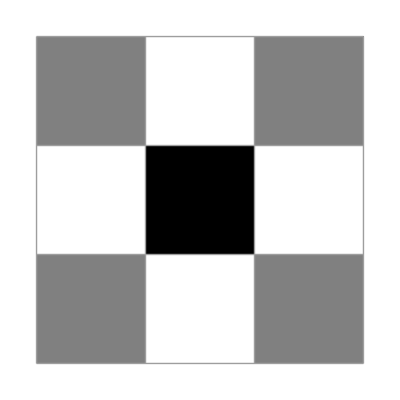

```mathematica
ArrayPlot[mat, Mesh-> All]
```

```mathematica
grid = Import["~/Downloads/power/power.mtx"]
```

```mathematica
Clear[grid]
```

```mathematica
grid
```

grid

```mathematica
Import["~/Downloads/power/power.mtx"]
```